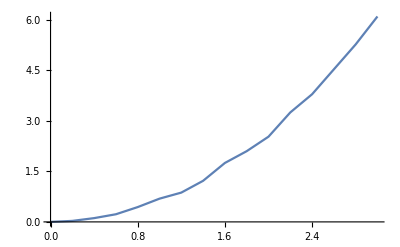

```mathematica
z = {0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2,2.2,2.4,2.6,2.8,3};
y={0,0.0295,0.112,0.227,0.44,0.69,0.87,1.22,1.75,2.1,2.53,3.25,3.79,4.53,5.27,6.1};
data=Transpose@{z,y};
ListLinePlot[data]
f[x_]:=a (x^2);
error = Table[f[z[[i]]] -y[[i]] ,{i,1,16}];
sum =0;
For[i=1,i<17,i++,
sum = sum + error[[i]]^2];
```

```mathematica
sum
```

(-0.0295+0.04 a)^2+(-0.112+0.16 a)^2+(-0.227+0.36 a)^2+(-0.44+0.64 a)^2+(-0.69+a)^2+(-0.87+1.44 a)^2+(-1.22+1.96 a)^2+(-1.75+2.56 a)^2+(-2.1+3.24 a)^2+(-2.53+4 a)^2+(-3.25+4.84 a)^2+(-3.79+5.76 a)^2+(-4.53+6.76 a)^2+(-5.27+7.84 a)^2+(-6.1+9 a)^2

```mathematica
Sqrt[sum]
```

√((-0.0295+0.04 a)^2+(-0.112+0.16 a)^2+(-0.227+0.36 a)^2+(-0.44+0.64 a)^2+(-0.69+a)^2+(-0.87+1.44 a)^2+(-1.22+1.96 a)^2+(-1.75+2.56 a)^2+(-2.1+3.24 a)^2+(-2.53+4 a)^2+(-3.25+4.84 a)^2+(-3.79+5.76 a)^2+(-4.53+6.76 a)^2+(-5.27+7.84 a)^2+(-6.1+9 a)^2)

```mathematica
NMinimize[Sqrt[sum],a]
```

{0.23622,{a→0.667792}}

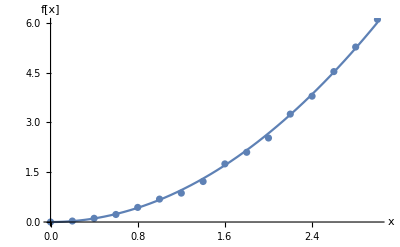

```mathematica
Show[Plot[0.6677916376912378x^2,{x,0,3},AxesLabel->{"x","f[x]"}],ListPlot[data]]
```

```mathematica
g[a_]=sum;

xold=2;
xnew=1;
While[xold-xnew>0.00000001,
xold=xnew;
xnew=xold-α g'[xold];
α=1;
While[g[xnew]-g[xold]>0,
α=α/2;
xnew=xold-α g'[xold];
];
];
xnew
```

0.672143